```mathematica
(*Some wavemeter calibration calculations*)
```

```mathematica
(*Constants*)
c=299792458;(*[m/s]*)
RSr88=109736.6308675;(*[cm^-1]*)
RSr87=109736.6230135;(*[cm^-1]*)
RSr86=109736.6149538;(*[cm^-1]*)
RSr84=109736.5982874;(*[cm^-1]*)
ISr88=45932.1982;(*[cm^-1]*)
ISr86=45932.1912;(*[cm^-1]*)
ISr84=45932.1833;(*[cm^-1]*)
```

```mathematica
(*Functions*)
δ[n_,δ0_,δ2_,δ4_]:=δ0+δ2/(n-δ0)^2+δ4/(n-δ0)^4;
ERyd88[n_,δ0_,δ2_,δ4_]:=ISr88-RSr88/(n-δ[n,δ0,δ2,δ4])^2;
ERyd86[n_,δ0_,δ2_,δ4_]:=ISr86-RSr86/(n-δ[n,δ0,δ2,δ4])^2;
ERyd84[n_,δ0_,δ2_,δ4_]:=ISr84-RSr84/(n-δ[n,δ0,δ2,δ4])^2;
```

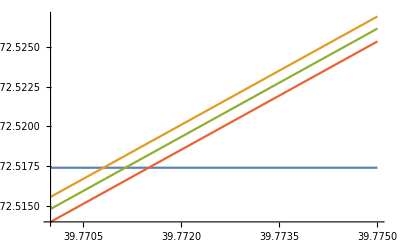

```mathematica
(*Molecular iodine line vs. strontium Rydberg lines*)
Eiodine=15672.517398;(*[cm^-1]*)
Ered88=(434829121311 10^3)(c)^-1(1/100);(*[cm^-1] 1S0-3P1 in 88Sr*)
Ered86=(434828957494 10^3)(c)^-1(1/100);(*[cm^-1] 1S0-3P1 in 86Sr*)
Ered84=(434828769718 10^3)(c)^-1(1/100);(*[cm^-1] 1S0-3P1 in 84Sr*)
Plot[{Eiodine,(ERyd88[n,3.371,0.5,-10]-Ered88)/2,(ERyd86[n,3.371,0.5,-10]-Ered86)/2,(ERyd84[n,3.371,0.5,-10]-Ered84)/2},{n,39.77,39.775}]
```